# V. 列表函数与函数式编程

## 5.1 前言

函数式编程是一种编程范式，函数的应用在其中扮演中心角色，应用的对象可以是数据也可以是其他函数。函数本身能被当作数据来看待，这样自然也能作为其他函数的参数。我们知道任何数据结构都能用列表（可能是嵌套的）表示，所以函数式编程与列表函数就密切相关了。

Mathematica中的函数式编程与其他函数式语言（LISP）有些很重要的不同。其中一点是，由于Mathematica中的列表是用数组而非链表实现的，表递归在Mathematica中的效率不是很高。另外一点不同是在函数定义（用模式定义函数时）和计算过程（全局规则库，表达式重写）中反映出来的以规则为基础（rule-based）的本质。

简单来说，函数式是Mathematica中最高效的编程风格。同时，虽然这一章不会提到，我们要知道在Mathematica里把函数式编程技术应用在比列表更通用的表达式上是可能的——应用于任意的表达式而不限于列表。这是很强悍的能力。

谈一谈这一章扮演的角色。也许说这一章是本书最重要的章节也不为过。这主要是因为本章介绍了新的编程风格和一些关于编程的新说法，这会在后续的章节中频繁使用，它们在一起构成了Mathematica编程的新水准。熟悉函数式编程的同学可能会感觉内容很熟悉。然而即使是对于这些同学，他们也能得到许许多多Mathematica中特有的信息，这些信息是高效编程的必需品。

本章行文中的的示例对于内容的阐述起很大的作用。很多例子被用来描述一些重要的概念和细微的差别，因为我认为任何新的知识在通过一些例子进行描绘后最容易被理解。为了完全搞懂本章，推荐读者细细看过每个例子，并留意例子旁的注释。我承认有些例子人工雕琢的味道很重，因为它们是用来以简单情境展示语言特性的。

## 5.2 核心高阶函数

### 5.2.1 简介

简单来说，Mathematica的函数式编程是由对普通表达式进行的函数应用组成的。一个特别的情况是当这里的普通表达式是一个列表（拥有头部List），在本章我们主要关注这种情况。然而，所有函数式编程能对列表做的事，几乎都能在普通表达式上实现。

有两件事让FP（函数式编程）变得非平凡：

1. 函数能将其他的函数作为参数（这和C里面的函数指针类似），在运行过程中也能创造或返回新的函数。这里的函数可以是纯函数或模式定义的函数，后者在过程式语言中没有直接的对应物——它们的函数定义是在编译过程中决定的。

2. 列表能由任意的Mathematica表达式组成——原子（数字、字符串、符号）或普通表达式。你可能会想到用嵌套列表来实现各种各样的数据结构（数组、树等等）。这也意味者一个列表能包含不同类型的对象。

这里还有几个关于函数式编程的特性我要简单提一下。其一，副作用（比如变量赋值）几乎是不会出现的；其二，循环结构很少被使用。在Mathematica里，循环不是被完全禁止的，只是使用另外一些结构将会更加自然，就如我们下面将看到的。

以其他函数作为参数的函数被称为高阶函数。概念上说，Mathematica中只有两个非常重要的高阶函数——Map和Apply。从实用层面上说，这两个函数仍然是最常用的高阶函数，但是还是有一些“不那么重要”的特殊内置函数存在着，它们用起来很方便。

我们将介绍一些最常用的高阶函数，举例说明其用法。它们是函数式编程的基本构件，仅仅掌握它们就能把你武装得很不错了！

### 5.5.5 Map——最简单的形式

Map是最基本的内置高阶函数之一，也是目前为止使用最为频繁的一个。简单说，它就是在FP中代替循环结构用的。

在最简单的形式，Map接收两个参数：一个单参数函数——让我们称之为f（我急不可耐的想强调一个纯函数是没有名字的，参见4.11节），一个表达式——我们称之为expr，它将被这个函数映射（map）。如果expr是个原子，它会被原样返回。

#### 5.2.2.1 最简单的用法

下面是一些最简单的例子：

```mathematica
Clear[f];
Map[f,a]
```

a

```mathematica
Map[f,{a,b,c}]
```

{f[a],f[b],f[c]}

上面的 f 没有任何定义，现在让我们给它些定义：

```mathematica
f[x_]:=x^2;
```

现在：

```mathematica
Map[f,{a,b,c}]
```

{a^2,b^2,c^2}

```mathematica
Map[f,a]
```

a

#### 5.2.2.2 Map是循环的替代品

现在让我们来看看Map是怎么代替循环的：在过程式版本中，对于上面的例子，我们大概需要这样写：

```mathematica
Module[{i,len,expr,newexpr},For[i=1;expr={a,b,c};
len=Length[expr];newexpr=Table[0,{len}],i <= len,i++,newexpr[[i]]=f[expr[[i]]]];
newexpr]
```

{a^2,b^2,c^2}

注意到在这里我故意把代码打包放在了Module里，这是为了让 i , expr 等变量局部化以及避免全局副作用。

所以，到这儿我们就可以看到Map的优势了：

不用引入附加的变量

不是事先知道列表的长度

代码更加精简

Map通常更快（虽然在这里看起来不是很明显）

事实上，Map的操作是在原列表的一个拷贝上进行的，原列表保持不变。

#### 5.2.2.3 在Map里使用纯函数

让我们重现原先的结果以示范如何在Map里使用纯函数：

```mathematica
Map[#^2&,{a,b,c}]
```

{a^2,b^2,c^2}

在这种情况下，函数名是多余的。另外，纯函数也会比模式定义的函数更快（特别是与Map联用时），因为没有发生模式匹配。但是，就如我们先前提到的，这也意味这对错误输入的防御会很少。

#### 5.2.2.4 缩写符与优先级

和很多常用操作一样，Map也有自己的缩写符——/@。用法是(function/@expression)。比如：

```mathematica
(f/@{a,b,c})
```

{a^2,b^2,c^2}

```mathematica
(#^2&/@{a,b,c})
```

{a^2,b^2,c^2}

你可以用Map也可以用/@。只要你在两边添上括号，它们的行为总是等价的，正如上面做的那样。在很多情况下，括号可以省略：

```mathematica
f/@{a,b,c}
```

{a^2,b^2,c^2}

```mathematica
#^2&/@{a,b,c}
```

{a^2,b^2,c^2}

通常情况下，为了避免优先级BUG，括号是必须的。比如，在下面的例子中，我们想先把f映射到列表上，然后对结果平方，我们在前缀符上用了一个纯函数（function@expression）。我们期望得到的结果是 {a^4, b^4, c^4} 。然而：

```mathematica
#^2&@f/@{a,b,c}
```

{f^2[a],f^2[b],f^2[c]}

呀，函数先被平方了，然后才映射。现在我们添上括号：

```mathematica
#^2&@(f/@{a,b,c})
```

{a^4,b^4,c^4}

当然，只要我们用Map这种问题就不可能发生：

```mathematica
#^2&@Map[f,{a,b,c}]
```

{a^4,b^4,c^4}

同时，完全形式Map也能让程序更加易读。我的建议是熟练以后再用/@。不过从实际应用上说，/@通常更加方便。

#### 5.2.2.5 结合规律

Map操作是右结合的，这意味着下面代码中的括号可以省略：

```mathematica
g/@g/@{a,b,c}
```

{g[g[a]],g[g[b]],g[g[c]]}

```mathematica
f/@f/@{a,b,c}       (*这里的<f>在上文中已经定义*)
```

{a^4,b^4,c^4}

#### 5.2.2.6 更多例子

现在让我们思考一些更有趣的例子。

这儿，将Range映射到一个Range产生的列表上，我们将得到一个深度为2的列表：

```mathematica
Map[Range,Range[4]]
```

{{1},{1,2},{1,2,3},{1,2,3,4}}

或者等价地：

```mathematica
Range/@Range[4]
```

{{1},{1,2},{1,2,3},{1,2,3,4}}

我们接收一个二维列表然后返回每个子列表的第一个元素：

```mathematica
Map[First,{{a,b},{c,d},{e,f},{g,h}}]
```

{a,c,e,g}

或者

```mathematica
First/@{{a,b},{c,d},{e,f},{g,h}}
```

{a,c,e,g}

下面的例子会接收一个二维列表作为参数，然后返回首层元素的所有子集：

```mathematica
Map[Subsets,{{a,b,c},{d,e}}]
```

{{{},{a},{b},{c},{a,b},{a,c},{b,c},{a,b,c}},{{},{d},{e},{d,e}}}

你可能早已意识到所有的例子都是一个用Map来实现的单重循环。这本身没什么大不了的，但是在更高的抽象层面上我们得到的好处是——我们再也不需要变量和赋值了，这样我们也用不着为它们操心了。例如：在这种方法中，我们再也不需要检查数组的边界了，同时也不会在性能上有丝毫损失！另外一个好处是结果的列表是通过Map在内部产生的，效率非常高！但是在过程式版本中，我们必须手动操作，这样效率很低（正如我们前面所提到的）。

#### 5.2.2.7 单参固定的多参函数的映射

让我们试想另一种情况：我们想Map一个多参函数，但是所有的参数中有一个参数是固定的。例如：

```mathematica
Clear[f,a];
f[x_,y_]:=Sin[x+y];
```

现在我们它Map到列表 { 1, 2, 3, 4, 5 } 上，让参数 y 的值固定为 a 。

也许这个问题最棒的解法是通过使用内置函数Thread。但是在这里为了举个例子，我们用Map来实现。

一种方法是定义附加函数 g：

```mathematica
Clear[g];
g[x_]:= f[x,a];
```

现在我们可以动用Map：

```mathematica
Map[g,Range[5]]
```

{Sin[1+a],Sin[2+a],Sin[3+a],Sin[4+a],Sin[5+a]}

在章节4.11.1.12，我们早已创造了一个科里化（curried）的函数。在那个例子里，函数是在局部产生的，没有名字或全局规则与之相联系。这是个值得记住的小窍门。但是，你要知道通常我们能用另外一个内置函数Thread（马上就会介绍）实现上面的功能，Thread专门为这种情况设计，而且可能会快一点。

```mathematica
Clear[f]                                         (*随手清变量是好习惯*)
```

#### 5.2.2.8 如何防止Map作用到整个列表上

我提到过Map的最简单形式是作为循环结构的替代品。在过程式方法中，我们能用Break[]命令提前退出循环，让我们来讨论下用Map该怎么达到这种效果。

在Mathematica的计算模型中，最棒的编程风格是把对象当作一个整体来操作，尽量避免将其打成碎片。Map完全符合这个原则——无论列表多长，Map都能作用到整个列表上。如果我们想提前退出Map的话，我能想到的唯一方法是抛出（Throw）一个中断（exception）。然而，如果你想得到的结果是一个列表（直到中断被抛出），那么要不你就要引入附加变量，或者使用基于Reap-Sow的更复杂的技巧。Reap-Sow技巧会在第二部分详细介绍。

设想一个例子：我们想把平方运算map到一列随机数字上，但是一遇到非整数就停止，然后返回已经处理过的部分列表。

这是我们的随机列表：

```mathematica
testlist=RandomInteger[{-1,10},{15}]
```

{1,9,4,8,9,4,1,2,2,3,10,5,0,1,3}

这是一个解决办法:

```mathematica
Module[{result={}},Catch[
	Map[If[#>0,AppendTo[result,#^2],Throw[result]]&,
               testlist]]]
```

{1,81,16,64,81,16,1,4,4,9,100,25}

虽然从各个方面看这个解决方案都不是很理想，而且用到了没学过的命令（Catch-Throw），有两件事我需要说明：

虽然内置函数Map本身没有在中途停止映射的用法，但是我们确实可以通过一些技巧来防止其作用到整个列表上。

做到这一点所付出的代价是很大的：

引入了变量result（还要用Module结构将其局部化）。

让所要映射的函数更加复杂（包含If命令）。

result在计算过程中不断地被追加（AppendTo）——大型列表中这种操作会很慢！对于最后一点，代码虽然能奏效但是太复杂了。

我们丢掉了Map给我们的自然好处：Map通常会自动为我们准备好结果列表。但是在这里我们引入了我们自己的结果列表result，不可避免地要比内置函数Map慢很多。事实上这里用Scan命令会更好，但是我们还没介绍到那里。

代码不够精简。

所以，我的建议是：设计一个这样的中断Map程序是不必要的。如果真的需要的话——用Trow和Catch组合（避免使用AppendTo——我们在后面会介绍更好的列表生成方法）。事实上，先Map到整个列表上然后再选出特定的元素通常会更高效。

#### 5.2.2.9 和过程式代码组合使用

我们可以通过植入过程式代码从而在一定程度上增强Map的能力。你可以把这看作函数的“运行时连续重定义”。不管怎么称呼，Mathematica可以很方便地做到这类事情。几个例子：

#### 5.2.2.9.1 示例：部分和

这样可以生成一个部分和数列：

```mathematica
Module[{sum=0},sum+=#&/@Range[10]]
```

{1,3,6,10,15,21,28,36,45,55}

或者定义一个函数：

```mathematica
Clear[partSum];
partSum[x_List]:=Module[{sum=0},sum+=#&/@x];
```

```mathematica
partSum[Range[15]]
```

{1,3,6,10,15,21,28,36,45,55,66,78,91,105,120}

#### 5.2.2.9.2 示例：模拟MapIndexed

这里我们将模仿函数MapIndexed的最简单形式（作用于平坦列表时）——它将列表元素的位置作为所要映射的函数的第二个参数。

```mathematica
Clear[f];
Module[
{pos=1},
f[#,{pos ++}]&/@Range[10,20]]
```

{f[10,{1}],f[11,{2}],f[12,{3}],f[13,{4}],f[14,{5}],f[15,{6}],f[16,{7}],f[17,{8}],f[18,{9}],f[19,{10}],f[20,{11}]}

我们可以将之打包成一个函数：

```mathematica
Clear[myMapIndexed];
myMapIndexed[f_,x_List]:=
	Module[{pos = 1},
            f[#,{pos ++}]&/@x];
```

#### 5.2.2.9.3 示例：重访移动平均数

我们可以实现一个新版本的移动平均数——在Map的计算过程中不断更新一个相邻元素列表。这里我们设计了一个作用在前15个自然数的函数，这个函数计算每个元素和左右两个相邻元素的平均值。

```mathematica
Module[
{avlist={},result},
CompoundExpression[
AppendTo[avlist,#];If[Length[avlist]≥5,result=Total[avlist]/5;
avlist=Rest[avlist];result]]&/@Range[15]]
```

{Null,Null,Null,Null,3,4,5,6,7,8,9,10,11,12,13}

下面照例将其打包成函数，我们可以删去前2 m个结果，因为它们会是Null：

```mathematica
Clear[movAverage];
movAverage[x_List,m_Integer]/;Length[x]>2 m:=
	Drop[Module[{avlist={},result},
		CompoundExpression[
			AppendTo[avlist,#];If[
				Length[avlist]≥2 m+1,
				result=Total[avlist]/(2m+1);
			avlist=Rest[avlist];result]]&/@x],2m];
```

试试：

```mathematica
Range[10]^2
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
movAverage[Range[10]^2,1]
```

{14/3,29/3,50/3,77/3,110/3,149/3,194/3,245/3}

下面是另一种将副作用的使用推向极致的实现：

```mathematica
Clear[movAverageAlt];
movAverageAlt[x_List,m_Integer]/;Length[x]>2m:=
	Module[{n=1},
       Total[Take[x,{n,2m+n++}]]/(2m+1)&/@Drop[x,2m]];
```

注意到在这里我们定义的纯函数没有从所map的列表上提取任何信息——这是一个零参数的纯函数（参见章节4.11.1.11），我们需要的仅仅是正确的长度而已。C程序猿可能会担心｛n,2m+n++},因为结果取决于计算的先后顺序。在这里，结果是与平台无关的，因为平坦列表上的标准计算顺序总是从左到右的。

我们可以做一下效率测试：

```mathematica
movAverage[Range[100000],10];//Timing
```

{1.68481,Null}

```mathematica
movAverageAlt[Range[100000],10];//Timing
```

{0.7176,Null}

可以看到第二种实现快了将近两倍。其实这两种实现的效率都不是很高，我们的目的只是演示Map的用法而已。

在章节 3.8.12，我们提到过最快的实现之一：

```mathematica
Clear[movingAverage ];
movingAverage[x_List,m_Integer]:=
	(Plus@@#)/Length[#]&@Partition[x,Length[x]-2m,1];
```

```mathematica
movingAverage[Range[100000],10];//Timing
```

{0.0936,Null}

通常，在Map里用上一两个有副作用的全局变量不会造成太大的效率损失。但是，如上所示，对于整个列表的操作（比如AppendTo）通常很费时间，这应该尽可能避免。

#### 5.2.2.10 Map的更普遍用法——作用于表达式的特定层次

Map把第三个可选参数作为层次指定。这里的层次指定用来确定函数应该作用于列表的哪一层，指定的表示方法和很多Mathematica结构中通用的层次指定法（参见章节1.1.7)一样。略加回忆即可知：单个的整数n表示从第一层到第n层都将被map；带括号的整数{n}表示只有第n层会被map；一对整数{m,n}表示从第m层map到第n层。

#### 5.2.2.10.1 初始化示例

```mathematica
Clear[f,testexpr];
```

我们的初始化列表：

```mathematica
testexpr=Outer[List,Range[2],Range[3]]
```

{{{1,1},{1,2},{1,3}},{{2,1},{2,2},{2,3}}}

首先我们试试Map最简单的用法：

```mathematica
Map[f,testexpr]
```

{f[{{1,1},{1,2},{1,3}}],f[{{2,1},{2,2},{2,3}}]}

现在让我们试着Map得更深一点，即穿过一些大括号之后再Map。

Map第一层和第二层：

```mathematica
Map[f,testexpr,2]
```

{f[{f[{1,1}],f[{1,2}],f[{1,3}]}],f[{f[{2,1}],f[{2,2}],f[{2,3}]}]}

这样也灵：

```mathematica
Map[f,testexpr,{1,2}]      (*层次指定 2 和 {1,2}是等价的*)
```

{f[{f[{1,1}],f[{1,2}],f[{1,3}]}],f[{f[{2,1}],f[{2,2}],f[{2,3}]}]}

这次只Map第三层：

```mathematica
Map[f,testexpr,{3}]
```

{{{f[1],f[1]},{f[1],f[2]},{f[1],f[3]}},{{f[2],f[1]},{f[2],f[2]},{f[2],f[3]}}}

也可以用负层次。比如在这里-1和3是等价的：

```mathematica
Map[f,testexpr,{-1}]
```

{{{f[1],f[1]},{f[1],f[2]},{f[1],f[3]}},{{f[2],f[1]},{f[2],f[2]},{f[2],f[3]}}}

对于嵌套的列表，如果子列表的维数都相同的话，我们倾向于使用正层次指定，因为每一层上的子元素都有相同的深度。但是从普遍意义上说，这种倾向是不存在的。

#### 5.2.2.10.2 不那么简单的例子——用Map排序嵌套列表的子列表

先生成一个深度为4的随机列表：

```mathematica
Clear[testexpr];
testexpr=Table[Random[Integer,{1,10}],{3},{2},{3}]
(*在6以后的版本中也可写为：
RandomInteger[{1,10},{3,2,3}]
*)
```

{{{4,6,10},{2,2,1}},{{6,8,2},{6,8,10}},{{3,7,7},{7,7,7}}}

现在我们要对每个子数组进行排序。现在的方法是将Sort函数Map到包含三元数组的那一层：

```mathematica
Map[Sort,testexpr,{2}]
```

{{{4,6,10},{1,2,2}},{{2,6,8},{6,8,10}},{{3,7,7},{7,7,7}}}

如果我们想降序排列的话：

```mathematica
Map[Sort[#,#1≥#2&]&,testexpr,{2}]
```

{{{10,6,4},{2,2,1}},{{8,6,2},{10,8,6}},{{7,7,3},{7,7,7}}}

这个例子用了点小技巧，有些东西需要稍加解释：Sort本身就是一个高阶函数，它的第二个可选参数能指定排序标准函数。排序标准函数，在这里即#1>=#2&，依赖于两个变量。Sort的参数#和排序标准函数的#1、#2直接不会发生混淆，因为后者完全包含于前者。下面我们换一种不用纯函数的方法，以示明晰：

```mathematica
Clear[sortF,critF];
critF[x_,y_]:=x≥y;
sortF[x_List]:=Sort[x,critF];
```

现在可以用sortF代替Sort：

```mathematica
Map[sortF,testexpr,{2}]
```

{{{10,6,4},{2,2,1}},{{8,6,2},{10,8,6}},{{7,7,3},{7,7,7}}}

明晰所付出的代价是必须引入并命名两个辅助函数。其实在这里我们可以使用内置函数GreaterEqual来代替critF：

```mathematica
result=Map[Sort[#,GreaterEqual]&,testexpr,{2}]
```

{{{10,6,4},{2,2,1}},{{8,6,2},{10,8,6}},{{7,7,3},{7,7,7}}}

前面的两个解法是用来展示通常情况下应该怎么做——在没有内置函数的时候。当然，如果有内置函数的话，肯定是直接用内置函数好些。

继续我们的例子。假如每个子数组也要根据首元素的大小来排序该怎么办？比如：{ {3, 1}, {5, 6, 7}, {2, 8}, {4, 6} }应该得到{ {2, 8}, {3, 1}, {4, 6}, {5, 6 7} }。这里的排序标准函数应该写为 #1[[1]]<=#2[[2]]&，然后Map至第一层：

```mathematica
result1=Map[Sort[#,#1[[1]]≤#2[[1]]&]&,result]
(*6以后的版本中可以写为
 Map[SortBy[#,First]&,result]
*)
```

{{{2,2,1},{10,6,4}},{{8,6,2},{10,8,6}},{{7,7,3},{7,7,7}}}

最后我们可能想把最高层的子列表也排序一下，根据其包含数字的总和。

#### 子问题：求一个嵌套数组的总和

例如，拿出第一个子列表：

```mathematica
sublist=result[[1]]
```

{{10,6,4},{2,2,1}}

求总和的最佳方式是首先用Flatten压平，去掉多余的括号，然后在结果上使用Total：

```mathematica
numsum=Total[Flatten[sublist]]
```

25

现在我们知道了如何求和，我们可以把学到的知识转化为一个纯函数（排序标准）：Total[Flatten[#1-#2]]>=0&（这里的子列表拥有相同的结构所以可以直接相减）

```mathematica
result2=Sort[result,Total[Flatten[#1-#2]]≥0&]
```

{{{8,6,2},{10,8,6}},{{7,7,3},{7,7,7}},{{10,6,4},{2,2,1}}}

注意，这里我们没再使用Map，因为我们所操作的层次Sort直接可以达到。

让我再次总结一下目的和代码：我们有一个层数为4的数字列表，我们想将其按照一下规则排序：最内层的自列表按降序排列；次内层的列表按照首元素的大小排序；最外层的子列表按照数字的总和排列。排序必须从最内层开始（某些情况下，顺序是无关的）。我们把上面的过程打包成一个函数，并把中间变量局部化。

```mathematica
Clear[sortNested];
sortNested[x_List]:=
	Module[{result,result1,result2},
	result=Map[Sort[#,GreaterEqual]&,x,{2}];
	result1=Map[Sort[#,#1[[1]]≤#2[[1]]&]&,result];
	result2=Sort[result1,Total[Flatten[#1-#2]]≥0&]]
```

看看效果：

```mathematica
sortNested[testexpr]
```

{{{8,6,2},{10,8,6}},{{7,7,3},{7,7,7}},{{2,2,1},{10,6,4}}}

这里给我们的启示是，为了可读性通常需要更多的附加代码。不要尝试写嵌套过深的函数，如sortNestedAlt。

此例告诉我们，通过使用纯函数、Map以及高阶函数能极大的缩减代码的规模，增强灵活性。并且，这也是Mathematica中最高效的方式。

### 5.2.3 MapAt

如果Map可以被看成一把机械手枪的话，那么MapAt就是一只精准的来复枪了。它能将函数作用到特定的位置上，而不是整个列表。

在最简形式下，MapAt需要三个参数：被映射的函数，目标表达式，将要被映射的元素的位置。如果只Map第一层的话，这里的位置仅仅是元素的索引即一个整数。通常，位置是有一系列标记组成的表。MapAt的位置指定方法和Position以及Extract相同。你也可以用MapAt同时作用在多个元素上，这时，第三个参数不再是单个的位置，而是一系列位置组成的表。这些位置所对应的元素可能在表达式的不同层，所以，表示位置的表可能有不同的长度。

#### 5.2.3.1 一些例子

```mathematica
Clear[ourlist];
```

```mathematica
ourlist={a,b,c,d}
```

{a,b,c,d}

假如我们想把Sin作用到第二个元素上：

```mathematica
MapAt[Sin,ourlist,2]
```

{a,Sin[b],c,d}

这次是第二和第三个元素：

```mathematica
MapAt[Sin,ourlist,{{2},{3}}]
```

{a,Sin[b],Sin[c],d}

一定不要忘记里面的大括号。如果省略，Mathematica会认为我们想把Sin映射到一个位置我{2, 3}的单个元素上。但是ourlist里没有一个这样的位置（ourlist只有一层），所以这会导致一个错误。

```mathematica
MapAt[Sin,ourlist,{2,3}]
```

MapAt::partw: {a, b, c, d} 的部分 {2, 3} 不存在.

MapAt[Sin,{a,b,c,d},{2,3}]

现在生成一个嵌套的列表：

```mathematica
Clear[testexpr,f];
testexpr=Table[Random[Integer,{1,10}],{3},{2},{3}]
```

{{{1,9,2},{4,6,4}},{{4,3,3},{10,10,9}},{{4,10,7},{4,10,4}}}

想想下面的几个例子，试着弄懂为什么结果是这样的：

```mathematica
MapAt[f,testexpr,2]
```

{{{1,9,2},{4,6,4}},f[{{4,3,3},{10,10,9}}],{{4,10,7},{4,10,4}}}

```mathematica
MapAt[f,testexpr,{{2},{3}}]
```

{{{1,9,2},{4,6,4}},f[{{4,3,3},{10,10,9}}],f[{{4,10,7},{4,10,4}}]}

```mathematica
MapAt[f,testexpr,{3,2}]
```

{{{1,9,2},{4,6,4}},{{4,3,3},{10,10,9}},{{4,10,7},f[{4,10,4}]}}

```mathematica
Map[f,testexpr,{3,2}]
```

{{{1,9,2},{4,6,4}},{{4,3,3},{10,10,9}},{{4,10,7},{4,10,4}}}

基本上，搞懂上面例子只需格外注意追踪位置的踪迹就行了。比如：{2, 1, 1}就代表第二个元素的第一个元素的第一个元素。

#### 5.2.3.2 和Map联用

MapAt经常和Map联用。例如我们想把 f Map到每个子列表的第二个元素上。代码即为：

```mathematica
Map[MapAt[f,#,2]&,testexpr,{2}]
```

{{{1,f[9],2},{4,f[6],4}},{{4,f[3],3},{10,f[10],9}},{{4,f[10],7},{4,f[10],4}}}

注意这里我们必须在Map上加一个层次指定{2}，如果不加的话结果就不对了：

```mathematica
Map[MapAt[f,#,2]&,testexpr]
```

{{{1,9,2},f[{4,6,4}]},{{4,3,3},f[{10,10,9}]},{{4,10,7},f[{4,10,4}]}}

#### 5.2.2.3 和Position联用

MapAt和Position联用也是常有的事。我们想把一个函数f作用到一个表达式的特定位置上，前提是该位置上的表达式满足特定的条件。这用模式匹配的方法很容易做到。在函数式方法中，我们用Position先求出所需的位置，然后将所得的结果放入MapAt中。

比如我们想把 f Map到所有的偶数上，代码即为：

```mathematica
MapAt[f,testexpr,Position[testexpr,_?EvenQ]]
```

{{{1,9,f[2]},{f[4],f[6],f[4]}},{{f[4],3,3},{f[10],f[10],9}},{{f[4],f[10],7},{f[4],f[10],f[4]}}}

或者作用在3的倍数上：

```mathematica
MapAt[f,testexpr,Position[testexpr,x_/;Mod[x,3]==0]]
```

{{{1,f[9],2},{4,f[6],4}},{{4,f[3],f[3]},{10,10,f[9]}},{{4,10,7},{4,10,4}}}

#### 警告：性能陷阱

要意识到MapAt带来的效率陷阱：当你一次性将MapAt作用到很多很多的位置上时，MapAt可能会非常慢！请参见【附录C】的详细讨论。在一些情况下，MapAt的性能是能得到改善的——参见第6章的有关例子。

#### 5.2.3.4 应用：多重随机游走

我们可以用MapAt来实现多重随机游走，即每个行走者的位置都被相同的函数更新：

```mathematica
Clear[randomWalk];
randomWalk[x_]:=x+Random[Integer,{-1,1}];
```

假设我们有5名行走者，全都从0开始：

```mathematica
nwalkers=5;
startpositions=Table[0,{nwalkers}]
```

{0,0,0,0,0}

我们可以一个一个地去更新它们，或者每次随机抽取一个人更新。对于后一种情况，我们可以先生成一个从1到n的随机更新表。每个数字k代表第k个行走者。

```mathematica
totalupdates=50;
updatelist=Table[Random[Integer,{1,nwalkers}],{totalupdates}]
```

{1,2,1,4,3,3,4,1,2,2,1,4,1,3,1,1,5,1,4,2,4,4,1,4,3,1,1,5,2,3,3,2,4,2,5,5,1,4,2,3,1,5,2,5,2,3,5,4,3,2}

下面给出了5为行走者的位置演变（FoldList稍后会介绍）：

```mathematica
Short[result=FoldList[MapAt[randomWalk,#1,#2]&,
	startpositions,updatelist],10]
```

{{0,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0},{1,0,0,0,0},{1,0,1,0,0},{1,0,1,0,0},{1,0,1,0,0},{1,0,1,0,0},{1,1,1,0,0},{1,1,1,0,0},{2,1,1,0,0},{2,1,1,-1,0},{2,1,1,-1,0},{2,1,0,-1,0},{2,1,0,-1,0},{2,1,0,-1,0},{2,1,0,-1,1},{2,1,0,-1,1},{2,1,0,-2,1},{2,2,0,-2,1},{2,2,0,-2,1},{2,2,0,-1,1},{3,2,0,-1,1},{3,2,0,-2,1},{3,2,1,-2,1},{3,2,1,-2,1},{4,2,1,-2,1},{4,2,1,-2,0},{4,3,1,-2,0},{4,3,2,-2,0},{4,3,1,-2,0},{4,3,1,-2,0},{4,3,1,-1,0},{4,2,1,-1,0},{4,2,1,-1,-1},{4,2,1,-1,-2},{5,2,1,-1,-2},{5,2,1,-1,-2},{5,1,1,-1,-2},{5,1,2,-1,-2},{4,1,2,-1,-2},{4,1,2,-1,-1},{4,2,2,-1,-1},{4,2,2,-1,-1},{4,2,2,-1,-1},{4,2,3,-1,-1},{4,2,3,-1,-2},{4,2,3,0,-2},{4,2,4,0,-2},{4,1,4,0,-2}}

为了得到每个行走者的轨迹，我们需要将结果进行转置（Transpose）。然后我们可以用ListLinePlot函数来可是化结果：

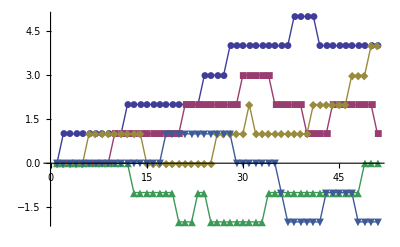

```mathematica
ListLinePlot[Transpose[result],PlotMarkers->Automatic]
(*
原书中所用的Graphics`MultipleListPlot函数在6版以后已经被
ListLinePlot等函数代替。
本文档在版本9下生成，所以用了更新后的函数
*)
```

#### 5.2.3.5 位置列表中的重复位置

如果位置列表中的某些位置重复了，那么函数会在此位置上应用多次（嵌套的）。比如：

```mathematica
Clear[g];
MapAt[g,Range[5],{{1},{2},{4},{2},{4},{4}}]
```

{g[1],g[g[2]],3,g[g[g[4]]],5}

然而，位置列表中位置的顺序并不会影响到函数应用的顺序。位置列表中的重复元素的在计算之前就已经被分组。我们可以通过引入一个计数器n来证明这一点：跟踪n的数值来确定计算的顺序是否与位置列表的顺序有关——结果是：无关。

```mathematica
MapAt[g[#,n++]&,n=0;Range[5],{{1},{2},{4},{2},{4},{4},{4}}]
```

{g[1,0],g[g[2,1],2],3,g[g[g[g[4,3],4],5],6],5}

这说明，在我们关于随机游走的例子中，不能把行走者的更新列表一下子扔给MapAt，因为计算的顺序会在内部被改变。

#### 5.2.3.6 映射的顺序

当MapAt作用在多个元素上的时候，我们早已知道实际的计算顺序是和位置列表的顺序不同的。那么，映射的顺序到底是怎么样的呢？答案是，位置列表会先被深度优先的方式重组。原因可能是这是避免歧义的唯一方法，因为原则上映射可能改变它所作用的子列表，甚至摧毁它。

#### 5.2.3.7 示例：模拟DeleteCases

一个很重要的情形是，我们经常会想根据一些标准来删除特定的元素。通常我们用DeleteCases达到这个目的。例如我们想从一嵌套列表里删除3的倍数。我们的试验列表是：

```mathematica
Clear[testexpr];
testexpr=Table[Random[Integer,{1,10}],{3},{2},{3}]
```

{{{2,8,10},{3,1,4}},{{7,7,4},{1,7,3}},{{2,4,8},{10,7,8}}}

我们可以通过映射函数#/.#:>Sequence[]&来模仿DeleteCases，其实就是将想删除的元素替换为“空”（如果你很迷惑的话，去试试只映射Sequence[]&会发生什么)。

```mathematica
MapAt[#/.#:>Sequence[]&,testexpr,Position[testexpr,x_/;Mod[x,3]==0]]
```

{{{2,8,10},{1,4}},{{7,7,4},{1,7}},{{2,4,8},{10,7,8}}}

使用Sequence[]&的情况（译者加）：

```mathematica
MapAt[Sequence[]&,testexpr,Position[testexpr,x_/;Mod[x,3]==0]]
```

Function::argb: Function 使用 0 个参数调用；预计有位于 1 和 3 之间个参数.

General::stop: 在本次计算中，Function :: argb 的进一步输出将被抑制.

{{{2,8,10},{Function[][3],1,4}},{{7,7,4},{1,7,Function[][3]}},{{2,4,8},{10,7,8}}}

打包成函数：

```mathematica
Clear[myDeleteCases];
myDeleteCases[expr_,patt_]:=
	MapAt[#/.#:>Sequence[]&,expr,Position[expr,patt]]
```

再试试：

```mathematica
myDeleteCases[testexpr,x_/;Mod[x,3]==0]
```

{{{2,8,10},{1,4}},{{7,7,4},{1,7}},{{2,4,8},{10,7,8}}}

如果用DeleteCases的话就是这样的（Infinity表示作用于所有的层次）：

```mathematica
DeleteCases[testexpr,x_/;Mod[x,3]==0,Infinity]
```

{{{2,8,10},{1,4}},{{7,7,4},{1,7}},{{2,4,8},{10,7,8}}}

### 5.2.4 MapAll

这个函数等同于Map[function, expression, {0, Infinity}]。层次指定里的0用来把函数应用到整个表达式上，这正是MapAll所做的。我们只举一个简单的例子：

```mathematica
Clear[testexpr,f];testexpr=Table[Random[Integer,{1,10}],{3},{2},{3}]
```

{{{6,7,8},{9,3,3}},{{6,10,10},{9,6,6}},{{1,4,1},{10,1,2}}}

```mathematica
MapAll[f,testexpr]
```

f[{f[{f[{f[6],f[7],f[8]}],f[{f[9],f[3],f[3]}]}],f[{f[{f[6],f[10],f[10]}],f[{f[9],f[6],f[6]}]}],f[{f[{f[1],f[4],f[1]}],f[{f[10],f[1],f[2]}]}]}]

#### 5.2.4.1 MapAll 采用深度优先的计算方法

容易证明，Map 在通用Mathematica表达式（都能用树状结构表示）上的映射采用深度优先的方法。为此我们考察下面嵌套列表（Fold 不久就会介绍）：

```mathematica
tst=Fold[List,{},{a,b,c,d}]
```

{{{{{},a},b},c},d}

这个函数打印并返回其参数：

```mathematica
ShowIt[x_]:=(Print[x];x)
```

把它映射到表达式的所有层上：

```mathematica
MapAll[ShowIt,tst]
```

{}

a

{{},a}

b

{{{},a},b}

c

{{{{},a},b},c}

d

{{{{{},a},b},c},d}

{{{{{},a},b},c},d}

这清楚地证明了映射的顺序是深度优先的。通常，当你想把一个函数应用到一个表达式的所有层并且希望其遍历的方式为深度优先（或者根本不关心遍历的顺序）的时候，应当使用 MapAll 。下面会有一个例子。

#### 5.2.4.2 与 ReplaceAll 联用

MapAll并不常用，但是至少在一个实例中是非常有用的——在进行规则替换时使规则以由内而外的顺序应用。这不是默认的工作方式。考虑下面的这条规则：

```mathematica
ourrule={x_,y_}:>{x,y^2};
```

现在我们尝试进行替换：

```mathematica
tst/.ourrule
```

{{{{{},a},b},c},d^2}

```mathematica
tst/.ourrule/.ourrule
```

{{{{{},a},b},c},d^4}

可以看到，规则总是应用在最外层，因为最外层被匹配了。一种明显的解决方法是对规则进行限制，即，让规则不匹配已经被转换过的表达式：

```mathematica
ournewrule={x_,y_/;Not[MatchQ[y,Power[_,2]]]}:>{x,y^2};
```

```mathematica
tst/.ournewrule
```

{{{{{},a},b},c},d^2}

```mathematica
tst/.ournewrule/.ournewrule
```

{{{{{},a},b},c^2},d^2}

```mathematica
tst//.ournewrule
```

{{{{{},a^2},b^2},c^2},d^2}

如上所示，我们成功地让我们的规则由外而内地进行了应用，很像剥洋葱。但这并不总是我们期望的行为。可以通过 MapAll 改变这种情况：MapAll 的深度优先性质可以让替换过程从最内层开始。我们可以用 Trace 命令监视此计算的过程（这里对Trace命令进行了限制使其只显示计算树中有关规则替换的部分）。

```mathematica
Trace[MapAll[#/.ourrule&,tst],ReplaceAll]
```

{{{{{{{{{{}/.ourrule,{}/.{x_,y_}:>{x,y^2},{}},{a/.ourrule,a/.{x_,y_}:>{x,y^2},a}},{{},a}/.ourrule,{{},a}/.{x_,y_}:>{x,y^2},{{},a^2}},{b/.ourrule,b/.{x_,y_}:>{x,y^2},b}},{{{},a^2},b}/.ourrule,{{{},a^2},b}/.{x_,y_}:>{x,y^2},{{{},a^2},b^2}},{c/.ourrule,c/.{x_,y_}:>{x,y^2},c}},{{{{},a^2},b^2},c}/.ourrule,{{{{},a^2},b^2},c}/.{x_,y_}:>{x,y^2},{{{{},a^2},b^2},c^2}},{d/.ourrule,d/.{x_,y_}:>{x,y^2},d}},{{{{{},a^2},b^2},c^2},d}/.ourrule,{{{{{},a^2},b^2},c^2},d}/.{x_,y_}:>{x,y^2},{{{{{},a^2},b^2},c^2},d^2}}

#### 题外话：With的使用与性能提升

Trace 同时揭示了上面的计算并不是百分百高效的，因为其中规则的定义每次都要被重新计算。为了避免这种现象，我们用<With>把规则定义按原文植入到代码中：

```mathematica
Trace[With[{rule = ourrule},MapAll[#/.rule&,tst]],ReplaceAll]
```

{{{{{{{{{{}/.{x_,y_}:>{x,y^2},{}},{a/.{x_,y_}:>{x,y^2},a}},{{},a}/.{x_,y_}:>{x,y^2},{{},a^2}},{b/.{x_,y_}:>{x,y^2},b}},{{{},a^2},b}/.{x_,y_}:>{x,y^2},{{{},a^2},b^2}},{c/.{x_,y_}:>{x,y^2},c}},{{{{},a^2},b^2},c}/.{x_,y_}:>{x,y^2},{{{{},a^2},b^2},c^2}},{d/.{x_,y_}:>{x,y^2},d}},{{{{{},a^2},b^2},c^2},d}/.{x_,y_}:>{x,y^2},{{{{{},a^2},b^2},c^2},d^2}}

注意，使用 Module 或 Block 不会达到同样的效果（植入），所以在这里也帮不了我们。

同样的功能可用层次指定为｛0，Infinitely} 的Replace达到，而不必用ReplaceAll：

```mathematica
Trace[Replace[tst,ourrule,{0,Infinity}]]
```

{{tst,{{{{{},a},b},c},d}},{ourrule,{x_,y_}:>{x,y^2}},{{∞,∞},{0,∞}},Replace[{{{{{},a},b},c},d},{x_,y_}:>{x,y^2},{0,∞}],{{{{{},a^2},b^2},c^2},d^2}}

这实则为一种更高效的解法，因为更多的操作在内核内部进行。但是，如果没有前面的讨论，ReplaceAll[expr, rules]和Replace[expr, rules, {0, Infinity}] 之间的区别就和一个迷一样了。很多情况下预期的行为是后者那样的，即由内而外地应用规则。

同时，就算在上面所说的那种情况下（计算需要由内而外进行），使用形如 MapAll[# /. rules&, expr]的结构也是有利的，因为它和 Replace[expr, rules, {0, Infinity}] 的功能完全一样且允许更为细致的追踪和调试。一旦代码测试（或调试）成功，便可将其变回 Replace[expr, rules, {0, Infinity}] 。

最后一点，有时可能需要将规则重复作用在每一层上直到被作用的表达式不再改变。这可以用 MapAll[ReplaceRepeated[#, rules]&, expr]做到，不过就我所知，没有用Replace实现此功能的简单方法。

### 5.2.5 Scan

Scan 和 Map 类似，不同的是它不会在计算的最后返回结果列表。这意味着 Scan 只有在参函数包含副作用（比如赋值）的时候才会起作用。格式是：

Scan[f, expr, levspec]，

其中<f>是被scan的函数，<expr>是被<f>scan的表达式，<levspec>是个可选的层次指定——语法和 Map 很类似。

#### 5.2.5.1 简单示例

举个小例子，比如将乘方函数 scan 到一个列表上：

```mathematica
Scan[#^2&,Range[10]]
```

可以看到，没有输出生成（或者更精确的说，输出的是Null）。为了让其起到一点作用，我们需要一些副作用。比如这里我们用 Scan 计算列表元素的平方和：

```mathematica
Module[{sumsq = 0}, Scan[
                         sumsq+=#^2&, Range[10]
                         ];
                    sumsq
       ]
```

385

因为 Scan 并不返回结果列表，某种程度上它比 Map 更快。然而，两者之间还有另一个，并且可能更重要的区别：Scan能在任意的时刻被“停止”，通过参函数内部的 Return 语句。这对 Map 不成立——它只能被抛出的中断停止。例如我们想依次计算一列数字的平方和，直到某个位置元素大于6：

```mathematica
Module[{sumsq=0},
Scan[If[#≤6,sumsq+=#^2,Return[sumsq]]&,
Range[10]
]
]
```

91

Return 语句只能跳出 Scan，不能跳出 Scan 外层的局部结构（比如上面的Module）。

#### 5.2.5.2 示例：条件列表拆分

Scan 也可被看作循环的替代品。比如在这里我们用它来决定在哪个位置将列表分为两部分（在条件<cond>首次满足时）。

```mathematica
Clear[splitWhen];
splitWhen[x_List, cond_] := Module[{n = 0},
	Scan[If[cond[#], Return[],n ++]&, x];{Take[x, n], Drop[x, n]}]
```

Scan 是比单重循环更好的选择，因为它是被优化过的且通用性更好：它能接受标准层次指定并可作用于通用符号树（Mathematica表达式）而不仅仅是简单的一维列表。尤其值得注意的是，它以深度优先的方式遍历表达式，计算我们指示的任意副作用。

### 5.2.6 MapIndexed

这是个很有用的函数，它一定程度上扩展了Map的能力。你可能遇到这样的情况：一方面，你需要类似于Map的功能；另一方面，Map又不能完全胜任该任务。有时，我们需要知道被Map的函数在列表中的当前位置。接下来看过例子。

#### 5.2.6.1 语法与基础例子

比方说我们有个简单的数字列表：

```mathematica
testlist=Table[Random[Integer,{0,10}],{15}]
```

{6,5,8,4,9,2,10,5,9,7,10,3,5,1,3}

现在假如我们想把函数 (（-1）)^n Sin[x] map到这个列表上，其中 n 代表当前列表元素的位置，x 是当前的列表元素。对于这个简单的例子，我们可以用Map做到：

```mathematica
Module[{n=0},
Map[(-1)^(n ++)Sin[#]&,testlist]]
```

{Sin[6],-Sin[5],Sin[8],-Sin[4],Sin[9],-Sin[2],Sin[10],-Sin[5],Sin[9],-Sin[7],Sin[10],-Sin[3],Sin[5],-Sin[1],Sin[3]}

然而这不是个优雅的解法。同时，对于更复杂的列表此方法也无能为力。MapIndexed能给所map的函数是提供第二个参数以表示当前元素的位置。所以，和Map不同的是，MapIndexed所接收的函数必须有两个参数，其余的语法是一样的：

MapIndexed[function, expression, level ]

和以前一样，层次指定<level>也是一个默认为 1 的可选参数。对于这个例子，我们可以这样写：

```mathematica
MapIndexed[(-1)^#2[[1]] Sin[#1]&,testlist]
```

{-Sin[6],Sin[5],-Sin[8],Sin[4],-Sin[9],Sin[2],-Sin[10],Sin[5],-Sin[9],Sin[7],-Sin[10],Sin[3],-Sin[5],Sin[1],-Sin[3]}

注意到这里也用到了纯函数，两个参数的纯函数。同时也注意到我们提取了第二个参数的第一部分，#2[[1]]：这是因为元素的位置总是以索引列表给出的，即使对简单的列表也是这样。

原则上我们同样可以使用规则定义的函数：

```mathematica
Clear[g];
g[x_,{n_Integer}]:=
(-1)^n Sin[x];
MapIndexed[g,testlist]
```

{-Sin[6],Sin[5],-Sin[8],Sin[4],-Sin[9],Sin[2],-Sin[10],Sin[5],-Sin[9],Sin[7],-Sin[10],Sin[3],-Sin[5],Sin[1],-Sin[3]}

另外一个简单例子：将数字和其位置放在同一个列表里：

```mathematica
MapIndexed[List,testlist]
```

{{6,{1}},{5,{2}},{8,{3}},{4,{4}},{9,{5}},{2,{6}},{10,{7}},{5,{8}},{9,{9}},{7,{10}},{10,{11}},{3,{12}},{5,{13}},{1,{14}},{3,{15}}}

#### 5.2.6.2 更多例子

##### 5.2.6.2.1 示例：建立特定的矩阵

当扩展到嵌套的列表和树的时候，MapIndexed就能做更多不简单的事了。比如，我们可以建立一个元素为Sin[i - j]的矩阵（4 × 4)，其中 i 和 j 分别是列和行的标号：

```mathematica
(result = MapIndexed[Sin[#2[[1]]-#2[[2]]]&,
IdentityMatrix[4],{2}])//MatrixForm
```

(0 | -Sin[1] | -Sin[2] | -Sin[3]
Sin[1] | 0 | -Sin[1] | -Sin[2]
Sin[2] | Sin[1] | 0 | -Sin[1]
Sin[3] | Sin[2] | Sin[1] | 0)

这里我们map到了第二层，对应于单个数字。同时，参数#2就是列表元素的位置索引（i 和 j）。这个例子可以轻松地修改为——生成一个列表元素的位置矩阵：

```mathematica
MapIndexed[#2&,IdentityMatrix[4],{2}]
```

{{{1,1},{1,2},{1,3},{1,4}},{{2,1},{2,2},{2,3},{2,4}},{{3,1},{3,2},{3,3},{3,4}},{{4,1},{4,2},{4,3},{4,4}}}

又比如我们想将主对角线上下的两条对角线的元素变为一个不确定的 <a>。代码如下：

```mathematica
(result1=MapIndexed[
If[Abs[#2[[1]]-#2[[2]]]==1,a,#1]&,result,{2}])//MatrixForm
```

(0 | a | -Sin[2] | -Sin[3]
a | 0 | a | -Sin[2]
Sin[2] | a | 0 | a
Sin[3] | Sin[2] | a | 0)

在这个特定的例子里，基于MapIndexed 的例子并不是很高效，因为对于大部分被测试的元素我们已经预先知道其不在对角线上了。本章后面将会给出更高效的方法，此方法基于MapThread。

同时注意到原则上这里的方法可以扩展至任意矩阵的生成。我们需要做的只是定义一个以当前位置计算其矩阵元素的函数就行了，然后这个函数能被MapIndexed利用。另外我们还需要一个初始矩阵（这里我们用的是单位矩阵IdentityMatrix）。

##### 5.2.6.2.2 生成并操纵函数矩阵

我们还可以做更多有趣的事情。比如生成一个所有元素都是函数的矩阵：

```mathematica
(result3=MapIndexed[x^Total[#2]&,IdentityMatrix[3],{2}])//MatrixForm
```

(x^2 | x^3 | x^4
x^3 | x^4 | x^5
x^4 | x^5 | x^6)

我们能求其行列式的符号结果：

```mathematica
Det[result3]
```

0

找到对角线上的元素，并对其求积分，其余的元素求微分：

```mathematica
(result4=MapIndexed[
Simplify[If[#2[[1]]==#2[[2]],Integrate[#1,x],D[#1,x]]]&,result3,{2}])//MatrixForm
```

(x^3/3 | 3 x^2 | 4 x^3
3 x^2 | x^5/5 | 5 x^4
4 x^3 | 5 x^4 | x^7/7)

##### 5.2.6.2.3 示例：模仿Position命令

可以用MapIndexed来模仿Position命令：

```mathematica
Clear[testexpr]
testexpr=Table[Random[Integer,{1,10}],{3},{2},{3}]
```

{{{1,10,1},{1,10,4}},{{1,7,2},{6,4,9}},{{7,4,4},{10,2,8}}}

现在找出所有能被3整数的元素的位置：

```mathematica
Flatten[MapIndexed[
If[Mod[#1,3]==0,#2,#1/.#1:>Sequence[]]&,testexpr,{3}],2]
```

{{2,2,1},{2,2,3}}

```mathematica
Clear[g,result,result1,result3,result4,testexpr]
```

##### 5.2.6.2.4 示例：模仿Partition命令

比方说有个数字列表，我们想把它分割成几个子列表（为了简明这里不考虑嵌套的情况。通常这个操作有Partition命令来完成，但我们也可以用MapIndexed模拟其行为。

```mathematica
Clear[testlist]
testlist=Table[Random[Integer,{1,10}],{15}]
```

{9,2,7,5,8,9,2,10,2,2,2,9,6,5,9}

我们需要将其分割成长度为4的子列表（剩下的三个数字被丢掉）。预先生成列表结构：

```mathematica
struct=Table[0,{IntegerPart[15/4]},{4}]
```

{{0,0,0,0},{0,0,0,0},{0,0,0,0}}

然后请来MapIndexed：

```mathematica
MapIndexed[testlist[[#2[[2]]+(#2[[1]]-1)*4]]&,struct,{2}]
```

{{9,2,7,5},{8,9,2,10},{2,2,2,9}}

将上面的操作打包成一个函数：

```mathematica
Clear[myPartition];
myPartition[lst_List,size_Integer]:=
Module[{len=Length[lst],struct},
struct = Table[0, {IntegerPart[len/size]}, 
	{size}];
MapIndexed[lst[[#2[[2]]+(#2[[1]]-1)*size]]&
	, struct, {2}]]
```

测试：

```mathematica
myPartition[testlist,4]
```

{{9,2,7,5},{8,9,2,10},{2,2,2,9}}

```mathematica
myPartition[testlist,3]
```

{{9,2,7},{5,8,9},{2,10,2},{2,2,9},{6,5,9}}

```mathematica
myPartition[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

跟内置函数比较的结果蛮有趣：

```mathematica
myPartition[Range[400000],3];//Timing
```

{1.90321,Null}

```mathematica
Partition[Range[400000],3];//Timing
```

{0.0156,Null}

不出所料，我们差的可不止一点哩（在我的机子上慢了上百倍）！虽然肯定还有比这更糟的实现方法。从实际应用角度来说，这又一次印证了这条规则：尽可能地使用内置函数，并由此构建程序。

##### 5.2.6.2.5 示例：不排序的Union

本例设计的技巧是通过MapIndexed生成一系列的规则。我们的目标是计算一列表中的对象在未经排列情况下的合并（Union）。先回想一下前面的内容：Union命令返回所给列表中所有相异元素排序后的结果。即，先去重，后排序。（参见章节3.10.2）例如：

```mathematica
Union[{b,c,a,d,c,d,a,c,b}]
```

{a,b,c,d}

现在我们期望我们定义的函数<unsortedUnion>同样可以删除重复项，但是随后不进行排序操作。比如，对于上面的例子其结果应该是：

```mathematica
{b,c,a,d}
```

{b,c,a,d}

我们目前的实现手段将基于规则的应用。以后还会降到另一个基于Reap-Sow技巧的实现方法，比目前的方法更加优雅。

这里的思路为：先生成一个形如｛元素1->位置1, 元素2->位置2.......} 的规则列表。然后我们用标准的Union获得所给列表去重并排列后的结果。然后将规则列表应用到前面得到的结果上，这样可以给出每个相异元素在列表中首次出现的位置（因为对于规则列表而言，只有第一次匹配某个元素的规则会被应用，然后规则会应用在接下来的元素上）。这样我们就得到了一个位置列表。剩下的事就是对位置列表进行排序然后抽取出相应的元素。别急，现在我们一步一步来：

这是用于测试的列表：

```mathematica
testlist=Table[Random[Integer,{1,10}],{20}]
```

{5,7,8,7,4,3,1,3,6,6,6,7,8,2,1,4,1,1,2,10}

用MapIndexed产生一组规则：

```mathematica
rules=MapIndexed[Rule,testlist]
```

{5→{1},7→{2},8→{3},7→{4},4→{5},3→{6},1→{7},3→{8},6→{9},6→{10},6→{11},7→{12},8→{13},2→{14},1→{15},4→{16},1→{17},1→{18},2→{19},10→{20}}

计算Union，应用规则：

```mathematica
un=Union[testlist]
```

{1,2,3,4,5,6,7,8,10}

```mathematica
un/.rules
```

{{7},{14},{6},{5},{1},{9},{2},{3},{20}}

排序：

```mathematica
Sort[un/.rules]
```

{{1},{2},{3},{5},{6},{7},{9},{14},{20}}

剩下的就是抽出对应的元素：

```mathematica
Extract[testlist,Sort[un/.rules]]
```

{5,7,8,4,3,1,6,2,10}

将所有的步骤组装，打包：

```mathematica
Clear[unsortedUnion];
unsortedUnion[x_List]:=
	Extract[x,Sort[Union[x]/.Dispatch[MapIndexed[Rule,x]]]];
```

Dispatch 命令会在后面介绍。现在你只需要知道它能让规则替换进行得快一点——对不能同时应用的规则建立哈希查找表。这对我们的函数尤为重要，因为所以关于重复元素的规则都能被Dispatch优化加速。等到介绍Dispatch的时候，我们会回顾此问题并以一个性能测试来确定我们从Dispatch那里捞到了多少好处。目前，就让我们瞧瞧这个函数灵不灵：

```mathematica
unsortedUnion[testlist]
```

{5,7,8,4,3,1,6,2,10}

```mathematica
Clear[testlist,list,un,unsortedUnion]
```

##### 5.2.6.2.6 示例：统计列表元素的频数

上个例子中MapIndexed、Dispatch和Union的组合用法同样可以用于计算列表元素的频数（在版本6以前，这项功能可在程序包Statistics`DataManipulation中找到，其实现方法用到了Split命令——我们在章节3.1 0.3.4介绍过这个实现。到了版本6.0，这项功能被内置的Tally所接替，速度更快）。

让我们来编制函数<frequencies>。测试用的列表如下：

```mathematica
testlist=Table[Random[Integer,{1,20}],{40}]
```

{13,1,8,10,5,20,18,12,5,6,4,20,17,16,11,18,8,11,10,8,8,1,20,9,6,13,20,19,19,11,7,10,15,19,10,9,5,9,9,13}

第一步和之前一样：为列表中Union过后得到的元素建立一个形如<元素->位置>的规则集合，然后用这些规则去将原始列表中所有元素替换为对应的位置：

我们的列表Union之后的结果：

```mathematica
un=Union[testlist]
```

{1,4,5,6,7,8,9,10,11,12,13,15,16,17,18,19,20}

规则集合：

```mathematica
rules=MapIndexed[Rule[#1,First[#2]]&,un]
```

{1→1,4→2,5→3,6→4,7→5,8→6,9→7,10→8,11→9,12→10,13→11,15→12,16→13,17→14,18→15,19→16,20→17}

用Dispatch加速后的替换列表将所有的元素替换为它们的位置。

```mathematica
replaced=ReplaceAll[testlist,Dispatch[rules]]
```

{11,1,6,8,3,17,15,10,3,4,2,17,14,13,9,15,6,9,8,6,6,1,17,7,4,11,17,16,16,9,5,8,12,16,8,7,3,7,7,11}

现在，生成一列计数器

```mathematica
counters=Array[0&,{Length[un]}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

然后把相应位置的自增运算Scan到我们前面得到的位置列表上：

```mathematica
Scan[counters[[#]]++&,replaced]
```

现在我们就把每种相异元素的个数数出来了：

```mathematica
counters
```

{2,1,3,2,1,4,4,4,3,1,3,1,1,1,2,3,4}

剩下要做的就是把<un>中的每个元素和对应的频数组合起来。这可以用另一个MapIndexed轻松实现，因为每个元素的频数在<counters>中的位置和元素在<un>中的位置是一样的。

```mathematica
MapIndexed[{#1,counters[[#2[[1]]]]}&,un]
```

{{1,2},{4,1},{5,3},{6,2},{7,1},{8,4},{9,4},{10,4},{11,3},{12,1},{13,3},{15,1},{16,1},{17,1},{18,2},{19,3},{20,4}}

将所有步骤打包成一个函数：

```mathematica
Clear[frequencies];
frequencies[x_List]:=With[{un=Union[x]},
	Module[{counters=Array[0&,{Length[un]}]},
		Scan[counters[[#]]++&,
			ReplaceAll[x,
				Dispatch[MapIndexed[Rule[#1,First[#2]]&,
					un]]]];
		MapIndexed[{#1,counters[[#2[[1]]]]}&,un]]];
```

测试:

```mathematica
frequencies[testlist]
```

{{1,2},{4,1},{5,3},{6,2},{7,1},{8,4},{9,4},{10,4},{11,3},{12,1},{13,3},{15,1},{16,1},{17,1},{18,2},{19,3},{20,4}}

作为对比，我们看看程序包Statistics`DataManipulation`里的实现方法。

```mathematica
Clear[frequenciesAlt];
frequenciesAlt[x_List]:=
	Map[{First[#],Length[#]}&,Split[Sort[x]]];
```

对比一下速度：

```mathematica
testlist=Table[Random[Integer,{1,200}],{100000}];
frequencies[testlist];//Timing
frequenciesAlt[testlist];//Timing
```

{0.2808,Null}

{0.0156,Null}

```mathematica
testlist=Table[Random[Integer,{1,200}],{400000}];
frequencies[testlist];//Timing
frequenciesAlt[testlist];//Timing
```

{1.18561,Null}

{0.0936,Null}

```mathematica
testlist=Table[Random[Integer,{1,200}],{1000000}];
frequencies[testlist];//Timing
frequenciesAlt[testlist];//Timing
```

{3.04202,Null}

{0.2184,Null}

大家可以看到基于Sort和Split的版本要快上很多倍。在这里我介绍这样一个更复杂且效率欠佳的实现是基于两方面的考虑。首先，这仍然是综合多种编程手段（过程式，函数式，规则）的良好范例；其次，这再次证明了某些通用的函数（比如Sort）是难以超越的，如果你的问题能被重构到可以借助它们威力的形式，使用这些内置函数总是有利的。

### 5.2.7 Apply

Apply是函数式编程范式中另一个最基础的高阶函数。它的行为和Map及其类似的函数不太一样。Apply以一个函数<f>作为第一个参数，一个表达式<expr>作为第二个参数。它将<expr>的替换为<f>。举几个简单的例子：

#### 5.2.7.1 简单示例

```mathematica
Clear[a,b,c];
Apply[List,a+b+c]
```

{a,b,c}

为了搞懂发生了什么，查看一下上面求求和式的内部形式：

```mathematica
FullForm[a+b+c]
```

Plus[a,b,c]

所以，头部Plus被替换为头部List了。再看几个例子：

```mathematica
Apply[Plus,a*b*c]
```

a+b+c

这次我们把头部Times替换成了Plus。现在考虑：

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

下面的命令可以给出前十个非零自然数之和：

```mathematica
Apply[Plus,Range[10]]
```

55

这个可以算出10！：

```mathematica
Apply[Times,Range[10]]
```

3628800

值得注意的是这种计算阶乘的方法几乎和内置的命令同样快：

```mathematica
Timing[Apply[Times,Range[100000]];]
```

{0.078,Null}

```mathematica
Timing[100000!;]
```

{0.0312,Null}

#### 5.2.7.2 缩写符号

作为另一个常用的操作，Apply也有一个简写的标记：<@@>。所以，为了把<f>Apply到<expr>上，可以写作：

```mathematica
（f@@expr）
```

（ ） expr

再次注意，外面的括号经常是可以省略的，但是为了避免和优先级相关的Bug，通常还是加上为好。

现在我们已经见识了足够了例子来搞懂真正需要Apply的情况：有时一些函数需要某些普通表达式的内部（比如，以逗号隔开的各个元素，但是不包括头部）。所以，Apply真正做的是把当前表达式的头部“吃掉”，然后用一个新的头部替代，那些被逗号隔开的部分都被新的头部继承。

#### 5.2.7.3 更多例子

##### 5.2.7.3.1 示例：计算任意秩张量的二次规范

这个例子我们以前就已经见过（参见章节 3.8.3.3），但是直到现在我们才能完全理解它。下面这个函数能计算任意秩张量的二次规范：

```mathematica
Clear[tensorNorm];
tensorNorm[tensor_List]:=Sqrt[Plus@@Flatten[tensor^2]]
```

它的工作方式如下：首先，这个列表被平方（很多内置函数，包括这里的Power，具有属性Listable（章节4.9.1），能自动应用到列表的每个层次上，所以平方一个嵌套的数字列表相当于平方列表中的每一个数字）。然后我们用Flatten将列表的嵌套结构展平。接着我们通过Apply的简写形式将头部List替换为Plus。最后，我对得到的结果求平方根。

例如，对于一个向量（列表）：

```mathematica
tensorNorm[Range[10]]
```

√385

对于一个3x4阶矩阵：

```mathematica
(matrix=Table[i+j,{i,1,3},{j,1,4}])//MatrixForm
```

(2 | 3 | 4 | 5
3 | 4 | 5 | 6
4 | 5 | 6 | 7)

```mathematica
tensorNorm[matrix]
```

√266

##### 5.2.7.3.2 示例：条件求和之偶数列表

考虑这个问题作为下一个例子：我们要写个对列表中数字进行求和的函数，但是此函数仅仅在列表中的所有数字都为偶数时才工作。如果此条件不满足，则返回未计算形式。

为了解这个问题，首先产生一个示例列表：

```mathematica
numlist=Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

对其求和简直不费吹灰之力：

```mathematica
Plus@@numlist
```

55

我们现在可以定义一个对任意列表求和的函数（这是为了举TMD例子，忽略内置函数Total吧）：

```mathematica
Clear[sumList];
sumList[x_List]:=Plus@@x;
```

试试灵不灵：

```mathematica
sumList[{1,2,3 ,4}]
```

10

现在我们得修改这个函数使其能对我们的条件进行判断。我们先单独写出写出这个条件。内置函数<EvenQ>能判断一个数是否为偶数。我们得对列表中的每一个数进行判断，所以必须将EvenQ Map到整个列表上（再一次为了TMD举例子，请无视EvenQ可以自动地遍历一个列表，让我们手动弄吧)。对于我们的列表：

```mathematica
Map[EvenQ,numlist]
```

{False,True,False,True,False,True,False,True,False,True}

剩下的就是将其嵌入到<And>中。但是<And>接受的参数不是一个表达式列表而是表达式序列（逗号隔开的那一溜玩意儿）。所以，此处的头部<List>必须被<And>“吃掉”，这意味这得用Apply：

```mathematica
Apply[And,Map[EvenQ,numlist]]
```

False

或者，其等价形式，

```mathematica
And@@Map[EvenQ,numlist]
```

False

最好一步是将条件插入到模式中：

```mathematica
Clear[sumListEven];
sumListEven[x_List]/;And@@Map[EvenQ,x]:=
		Plus@@x;
```

试试效果：

```mathematica
sumListEven[{2,4,6,8}]
```

20

```mathematica
sumListEven[{2,4,6,7,8}]
```

sumListEven[{2,4,6,7,8}]

注意这里条件模式操作符</;>的位置——它跟在参数列表的后面，而不是在里面。这通常是一个更好的习惯因为你可以为函数的多个参数设置条件。将参数检查放在参数列表的里面可能迫使Mathematica获得参数的全局值(而不是你传递过去的值)以进行参数检查，这通常不是你所期望的。

如果借用上面提到的EvenQ的Listable属性（自动应用到列表上）的话，代码看起来会更精简，更重要的是，更快：

```mathematica
Clear[sumList1];
sumList1[x_List]/;And@@EvenQ[x]:=Plus@@x;
```

让我们再添加一条定义吧。比如，对于奇数列表则求其乘积：

```mathematica
sumList1[x_List]/;And@@OddQ[x]:=Times@@x;
?sumList1
```

Global`sumList1

sumList1[x_List]/;And@@EvenQ[x]:=Plus@@x
 
sumList1[x_List]/;And@@OddQ[x]:=Times@@x

这条定义添加之后对于偶数列表的那条定义仍然被保留，然而咋看上去每条定义都包含同样的模式 sumList1[x_List]。为了解决这个矛盾（参见章节 4.7.3），你必须意识到在这里条件检查也是模式的一部分。所以，这两条定义对应的模式事实上是不同的。从DownValues可以清楚地看到这一点：

```mathematica
DownValues[sumList1]
```

{HoldPattern[sumList1[x_List]/;And@@EvenQ[x]]:>Plus@@x,HoldPattern[sumList1[x_List]/;And@@OddQ[x]]:>Times@@x}

最后提醒一句：在某些情况下，像这个问题里这般细致的参数检查可能会导致显著的性能开销，虽然看起来它们都是挺好写的。对于当前这个例子，我们被迫如此，因为这正是问题的陈述里所要求的。如果你正着手解决一个大型的问题，则整体的设计（如何将问题分散成子问题和函数）是你自己所决定的。在这种情况下，尽可能不要给每一个函数添加这样的条件检查，以避免冗余的判断（即传递过来的参数已经被确认合法了）。这就是我们“高效编程指导原则”的第四条：“避免繁杂的模式”。

```mathematica
Clear[numlist,sumList,sumList1,sumListEven];
```

##### 5.2.7.3.3 示例：包含给定字母的单词——编程实现“可选模式”

这个例子需要我们弄一些单词列表，比如这个（节选自《Mathematica全书》）：

```mathematica
wordlist={"Most","of","this","Part","assume","no","specific","prior","knowledge","of","computer","science","Nevertheless","some","of","it","ventures","into","some","fairly","complicated","issues","You","can","paobably","ignore","these","issues","unless","they","specifically","affect","programs","you","are","writing"};
```

现在给出问题：我们希望选出包含任一个特定字母的单词，这些字母由一个形如{“a”, ”n”, ”k”}的字母列表给出。

为了解决此问题，我们先从比较简单的情况开始，假使我们只有一个字母，比方说“a“。作为第一步，先写出判断单个单词是否包含特定字母的代码。我们先拿出一个单词：

```mathematica
ourword="fairly"
```

fairly

这里我不太想用字符串匹配之类的函数，所以第一件事就是将单词拆散成字母。完成此任务的最佳途径是内置命令<Characters>：

```mathematica
Characters[ourword]
```

{f,a,i,r,l,y}

现在我们需要判断给定的字母(“a”)是否属于这个列表。这次的最佳途径是<MemberQ>命令：

```mathematica
MemberQ[Characters[ourword],"a"]
```

True

我们现在期望将此衍生到多个字符的情况。一种方法是将MemberQ Map到列表上，然后使用内置的<Or>。假如第二个字母是”k”：

```mathematica
Map[MemberQ[Characters[ourword],#]&,{"a","k"}]
```

{True,False}

现在Apply一下<Or> (头部List被Or “吃掉”）：

```mathematica
Or@@Map[MemberQ[Characters[ourword],#]&,{"a","k"}]
```

True

我们已经准备好植入这个条件了，用Cases命令找出所有包含”a”或”k”的单词

```mathematica
Cases[wordlist,
x_String/;Or@@Map[MemberQ[Characters[x],#]&,{"a","k"}]]
```

{Part,assume,knowledge,fairly,complicated,can,paobably,specifically,affect,programs,are}

最后将一切打包成一个函数，此函数接受两个参数：一个单词列表和一个需要查找的字母列表：

```mathematica
Clear[findWordsWithSymbols];
findWordsWithSymbols[wlist_List,symbols_List]:=
	Cases[wlist,x_String/;Or@@Map[
MemberQ[Characters[x],#]&,symbols]];
```

注意我们将特定的字母列表换成了函数的参数<symbols>。让我找出所有包含”e”或者”r”的字母作为测试：

```mathematica
findWordsWithSymbols[wordlist,{"e","r"}]
```

{Part,assume,specific,prior,knowledge,computer,science,Nevertheless,some,ventures,some,fairly,complicated,issues,ignore,these,issues,unless,they,specifically,affect,programs,are,writing}

我们解决了这个问题，但是效率却不怎么样。就算从我们目前已经知道的支持来看，也存在一些优化的方法。最主要的低效之处在于<MemberQ[Characters[x], 3]&> 在字母列表上的映射。如果我们回忆起MemberQ的第二个参数是个模式的话，也就是说它不仅仅可以是一个字母，或许就能做得更好。具体来说，我们可以使用类似于”r”|”e”的可选模式，或者等价地，Alternatives[“a”, “k”]。

```mathematica
MemberQ[Characters[ourword],Alternatives["a","k"]]
```

True

再一次，因为我们的字母原先是放在一个列表里的，而Alternatives需要的是一个序列，头部<List>就必须被”Alternatives”吃掉，所以Apply就必不可少了：

```mathematica
MemberQ[Characters[ourword],Apply[Alternatives,{"a","k"}]]
```

True

或者，其等价形式，

```mathematica
MemberQ[Characters[ourword],Alternatives@@{"a","k"}]
```

True

现在可以重写我们的函数：

```mathematica
Clear[findWordsWithSymbolsAlt];
findWordsWithSymbolsAlt[wlist_List,symbols_List]:=
		Cases[wlist,x_String/;MemberQ[Characters[x],
			Alternatives@@symbols]];
```

测试：

```mathematica
findWordsWithSymbolsAlt[wordlist,{"n","m"}]
```

{assume,no,knowledge,computer,science,some,ventures,into,some,complicated,can,ignore,unless,programs,writing}

后一个版本效率更高的原因在于以下几点：后一种情况中，关于所给单词是否满足的“决定”在MemberQ这个层次上已经给出，然而在前一种情况，还需要另一个函数Or进一步处理。经验法则告诉我们，你必须尽可能一次性向一个内置函数倒入尽可能多的运算。MemberQ基本上不太在意它检查的是单一的字符还是有很多字母的可选模式（这是对于字母数较少的情况所说的）。另一方面，将MemberQ映射到每个字符上会迫使对每个字符进行检查。所以，我们可以粗略地认为影响性能的一个因素可能是字符列表长度的量级。测量字符列表为整个字母表时的时间可以说明我们的估计。我们将会用到测量极短时间用的<myTiming>函数（章节 3.4.5.2）。

```mathematica
alphabet=Characters["abcdefghijklmnopqrstuvwxyz"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
myTiming[findWordsWithSymbols[wordlist,alphabet]]
```

myTiming[{Most,of,this,Part,assume,no,specific,prior,knowledge,of,computer,science,Nevertheless,some,of,it,ventures,into,some,fairly,complicated,issues,You,can,paobably,ignore,these,issues,unless,they,specifically,affect,programs,you,are,writing}]

```mathematica
myTiming[findWordsWithSymbolsAlt[wordlist,alphabet]]
```

myTiming[{Most,of,this,Part,assume,no,specific,prior,knowledge,of,computer,science,Nevertheless,some,of,it,ventures,into,some,fairly,complicated,issues,You,can,paobably,ignore,these,issues,unless,they,specifically,affect,programs,you,are,writing}]

可以看到对于这次试验我们获得的性能提升可不止一个数量级（如果字符列表再短点的话可能差别就会小点）。作为副产品，我们的新函数不仅更加高效，而且更为精简和透明。在Mathematica中编程常常就是这样。我们的指导原则之一就是“程序越短，算得越快”（当然，例外是存在的）。

我们后面会看到人如何使这个函数更上一层楼，比方说在Reap-Sow的帮助下。

```mathematica
Clear[wordlist,findWordsWithSymbols,ourword,alphabet,findWordsWithSymbolsAlt]
```

##### 5.2.7.3.4 示例：提取矩阵的对角线

这里我们探讨如下问题：给定一个矩阵，我们需要提取它所有的右对角线（也就是从左上角到右下角的对角线），然后把它们放在一个列表里。这个问题将会在第六章详细探讨，在那里将会给出更加通用的三种解法。这里我们给出的是另一种（不是最高效的）基于多次重用MapIndexed和Apply的解法。事实上你将会看到这是一个综合多种已学技巧以及展示多个内置函数如何协同合作的良好范例。

我们的测试矩阵：

```mathematica
testmatr=Array[Random[Integer,{1,20}]&,{5,5}];
testmatr//MatrixForm
```

(9 | 9 | 3 | 8 | 4
19 | 18 | 7 | 8 | 17
10 | 3 | 9 | 13 | 18
17 | 11 | 13 | 4 | 4
3 | 16 | 15 | 5 | 7)

我们首先注意到对于任何一个右对角线，其中每个元素的索引值之差总是一个常数。这意味着我们可以用这个差值给每个矩阵元素打上“标签”，然后收集差值相同的那些元素。唯一值得担心的是我们得保证对角线元素是按正确的顺序收集的。幸运的是在这里MapIndexed遍历表达式的深度优先特性可以保证这一点。

好，让我们先从“打标签”开始：

```mathematica
step1=MapIndexed[{Subtract@@#2,#1}&,testmatr,{2}]
```

{{{0,9},{-1,9},{-2,3},{-3,8},{-4,4}},{{1,19},{0,18},{-1,7},{-2,8},{-3,17}},{{2,10},{1,3},{0,9},{-1,13},{-2,18}},{{3,17},{2,11},{1,13},{0,4},{-1,4}},{{4,3},{3,16},{2,15},{1,5},{0,7}}}

我们借助Apply将每个元素的位置列表的内部送给Subtract——也就是竖直及水平方向上的位置序列而不是列表（这正式MapIndexed提供给其映射函数的第二个参数）。同时也可以看到我们的映射必须指定在层次{2}，因为这里的操作是针对单个矩阵元素的。

此处还存在一些多余的括号，这些括号反映了原列表每行元素之间的分隔，但是我们现在不需要它们了。所以，让我们先Flatten一个层次：

```mathematica
step2=Flatten[step1,1]
```

{{0,9},{-1,9},{-2,3},{-3,8},{-4,4},{1,19},{0,18},{-1,7},{-2,8},{-3,17},{2,10},{1,3},{0,9},{-1,13},{-2,18},{3,17},{2,11},{1,13},{0,4},{-1,4},{4,3},{3,16},{2,15},{1,5},{0,7}}

现在我们以“标签”为基准将列表排序，以确保相同对角线上的元素是毗邻的：

```mathematica
step3=Sort[step2,First[#1]>First[#2]&]
```

{{4,3},{3,16},{3,17},{2,15},{2,11},{2,10},{1,5},{1,13},{1,3},{1,19},{0,7},{0,4},{0,9},{0,18},{0,9},{-1,4},{-1,13},{-1,7},{-1,9},{-2,18},{-2,8},{-2,3},{-3,17},{-3,8},{-4,4}}

注意这里我们用到了Sort的自定义排序标准的用法（在这里依据的是每个子列表的首个参数，即我们打的“标签”）。

这实际上是一个蛮有技巧的步骤，因为我们依靠的是Sort的一个特定工作方式：原则上无法保证在排序过程中不会打乱具有相同“标签”的元素的顺序。但是万幸，事实就是我们期望的那样。

作为最后一步，我们用Split将对应于同一条对角线的元素组合起来：

```mathematica
step4=Split[step3,First[#1]==First[#2]&]
```

{{{4,3}},{{3,16},{3,17}},{{2,15},{2,11},{2,10}},{{1,5},{1,13},{1,3},{1,19}},{{0,7},{0,4},{0,9},{0,18},{0,9}},{{-1,4},{-1,13},{-1,7},{-1,9}},{{-2,18},{-2,8},{-2,3}},{{-3,17},{-3,8}},{{-4,4}}}

接着将每个子列表的第二个元素(也就是原矩阵的元素）提取出来，同时保留组成对角线的大子列表的结构。这可以通过在嵌套列表的层次{2}上map第二个元素做到：

```mathematica
step5=Map[#[[2]]&,step4,{2}]
```

{{3},{16,17},{15,11,10},{5,13,3,19},{7,4,9,18,9},{4,13,7,9},{18,8,3},{17,8},{4}}

另一种（更高效的）途径是利用Part的一个扩展功能，即提取指令All：

```mathematica
step51=Part[step4,All,All,2]
```

{{3},{16,17},{15,11,10},{5,13,3,19},{7,4,9,18,9},{4,13,7,9},{18,8,3},{17,8},{4}}

由于我们在学函数式编程，我会在最后的实现中保留Map版本，但是要再一次说明，后一种方法更快，原则上更应该使用。（如果我们最终关心的是效率的话，我们一开始就应该选择一种不同的方法——详情参见第六章。同时，上面Sort的那种用户自定义排序函数的用法是没有被优化的。）

如你所见，上面得到的结果正是对角线，但是元素的顺序是反着的（传统上我们认为对角线应该从左上角开始）。所以，最后一件事就是将函数Reverse Map到对角线列表上：

```mathematica
result=Reverse/@step5
```

{{3},{17,16},{10,11,15},{19,3,13,5},{9,18,9,4,7},{9,7,13,4},{3,8,18},{8,17},{4}}

将一切打包成函数：

```mathematica
ClearAll[matrixRightDiags];
matrixRightDiags[matr_?MatrixQ]/;
		Equal@@Dimensions[matr]:=
		Map[Reverse,Map[#[[2]]&,Split[
			Sort[Flatten[MapIndexed[{Subtract@@#2,#1}&,matr,{2}],
				1],First[#1]>First[#2]&],
					First[#1]==First[#2]&],{2}]]
```

注意到我们用到了MatrixQ来判断输入的是否为矩阵，再用一个条件模式判断此矩阵是否为方阵——利用内置函数Dimensions获得矩阵的维度，再利用Apply“吃掉头部List还换以Equal以判断矩阵的两个维度是否相等。

好了，我们再来测试一次：

```mathematica
matrixRightDiags[testmatr]
```

{{3},{17,16},{10,11,15},{19,3,13,5},{9,18,9,4,7},{9,7,13,4},{3,8,18},{8,17},{4}}

本来原则上两个循环就能搞定的东西却这样写实在是太费功夫啦！信不信由你，实践中，在拥有一定经验的情况下，写出这样的函数是很快的。而且，比过程式更容易调试，因为每一行代码都进行了一次完整的转换并被独立测试。而且（从现在就坚定信念，或者先瞄一眼第六章），对于这个特定的问题，就算和目前这个欠高效的版本比起来，循环版本也是慢得要死。事实上，仔细想想便知，作用在层次{2}的MapIndexed也就相当于一个嵌套的迭代，但是这个迭代是在Mathematica内部进行的。最后要说明的是，这是一个复合了前面讨论过的多种技巧（条件模式、映射、层次指定、自定义的Sort和Split、纯函数）的良好范例。

作为作业，你可以考虑一下左对角线的情况（也就是从左下角到右上角的那些)。

#### 5.2.7.4 将参数序列提供给函数

我们讨论Apply的另一广泛用法。我们想把存储在一个单独的列表里的部分参数放到一个函数中使用。作为一个简单的例子，让我们定义一个有5个参数的函数，功能仅仅是把它们加起来。

```mathematica
Clear[addFive,x,y,z,t,s,a,b];
addFive[x_,y_,z_,t_,s_]:=x+y+z+t+s;
```

假设第一个和最后一个参数保持不变，也就是<a>和<b>。现在，给出一列三元数字列表：

```mathematica
testlist=Table[Random[Integer,{1,10}],{10},{3}]
```

{{1,9,2},{8,1,3},{2,3,8},{5,4,8},{7,1,7},{3,1,6},{10,6,4},{2,1,7},{1,2,9},{1,10,8}}

现在我们想将函数用到每个子列表上，这样子列表里的数字就能填补函数中间的三个空白参数。换句话说，我们想以一种有些特别的方式将函数Map到上面的列表上。按前面的讨论（章节5.2.2.7），一种方式是定义一个以三元数字列表为参数的辅助函数：

```mathematica
Clear[g];
g[lst_List]/;Length[lst]==3:=
	addFive[a,lst[[1]],lst[[3]],lst[[3]],b];
```

现在可以Map<g>

```mathematica
g/@testlist
```

{5+a+b,14+a+b,18+a+b,21+a+b,21+a+b,15+a+b,18+a+b,16+a+b,19+a+b,17+a+b}

这个解法的问题和我们之前讨论的那个类似的一样。之前，我们找到了一种运用纯函数的替代方法。在这里也行吗？先试试再说：

```mathematica
Map[addFive[a,#,b]&,testlist]
```

{addFive[a,{1,9,2},b],addFive[a,{8,1,3},b],addFive[a,{2,3,8},b],addFive[a,{5,4,8},b],addFive[a,{7,1,7},b],addFive[a,{3,1,6},b],addFive[a,{10,6,4},b],addFive[a,{2,1,7},b],addFive[a,{1,2,9},b],addFive[a,{1,10,8},b]}

我们几乎就要成功了。拦路虎是里面多余的头部List。我们知道Apply能移除一个表达式的头部。但是通常它会用新的头部代替，这里不应该这样。其实在Mathematica中存在着一个代表“没有头部”的特殊头部。这就是<Sequence>。这样，解法就是把Sequence Apply 一下：

```mathematica
Map[addFive[a,Sequence@@#,b]&,testlist]
```

{12+a+b,12+a+b,13+a+b,17+a+b,15+a+b,10+a+b,20+a+b,10+a+b,12+a+b,19+a+b}

这方法挺灵，而且有和前面提到的那个解法一样的优势(参见 5.2.2.7）。我迫不及待地要说一句，如果你需要Map到一个像这里一样的长列表上的话，有时会有更好的选择，例如Thread（下面介绍）。

```mathematica
Clear[addFive,g,testlist]
```